# Title

Reference (p.29):  http://ultracold.physi.uni-heidelberg.de/files/thesis%20friedhelm%20serwane.pdf

Usage: Edit the system parameters, run the calculation cells and see the results below.
See details below. Using the WKB approximation method in 1 dimension.

## Parameters

6.81818

{2.31437,5.08105,8.29995}

9.4749

0.105542

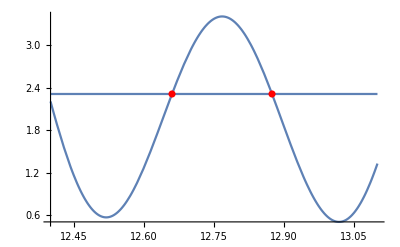

```mathematica
λ=1.064;
k=(2π)/λ;
grav=0.983; (*kHz per um*)
θxy=10.8Degree;

Vxy=30/4.4
Vz=15/4.4;

V[z_]:=Vxy*(1-Sin[k Sin[θxy] z]^2)+Vz*(1-Sin[k z]^2)

z1=12.2;
z2=z/.FindRoot[V'[z]==0,{z,12.7}];

ees=Table[ee/.FindRoot[NIntegrate[Re[k √(ee-V[z])],{z,z1,z2}]==π(n+1/2),{ee,2}],{n,0,2}]//Quiet

z2=z/.FindRoot[(V[z]==ee /. ee-> ees[[1]]),{z,12.65}];
z3=z/.FindRoot[(V[z]==ee /. ee-> ees[[1]]),{z,12.85}];
ssq=Exp[-2 NIntegrate[Re[k √(V[z]-ee)]/.ee-> ees[[1]], {z, z2, z3}]];
tau=2 2 π 1/(ees[[1]]*4.4)1/ssq
t=1/tau

pltx0=12.4;
pltx1=13.1;
Show[
Plot[V[z],{z,pltx0,pltx1}],
Plot[Evaluate[ees],{z,pltx0,pltx1}],
ListPlot[{{z2,V[z2]},{z3,V[z3]}},PlotStyle->Red]
]
```

## Calculations

Description of theory:

### Functions

```mathematica
findTunneling [potentialFunctionHz_, xMinGuess_,xMaxGuess_,mAtom_,nExcitedState_]:=Module[{smallXStep=0.001,hbar=1.05×10^-34,x,xMinFull,xMin,potentialMin,xMaxFull,xMax,potentialMax,xStart,potentialCurvatureGuess,energySymbolic,energyHz,realMomentum,x1,x2,x3,transmissionProbability,tunnelingRate},(* Finding the minimum of the given potential. xMinFull is an array of the minimum value and a rule giving the minimum location. *)
xMinFull=FindMinimum[{potentialFunctionHz[x],{x∈Reals}},{x, xMinGuess}];
xMin=x/.xMinFull[[2]];
potentialMin = xMinFull[[1]];
potentialCurvatureGuess=(potentialFunctionHz[xMin+smallXStep]+potentialFunctionHz[xMin-smallXStep]-2*potentialFunctionHz[xMin])/smallXStep^2;
(* Find the potential maximum between the two wells. xMaxFull is an array of the maximum value and a rule giving the maximum location. *)
xMaxFull=FindMaximum[{potentialFunctionHz[x],{x∈Reals}},{x,xMaxGuess}];
xMax=x/.xMaxFull[[2]];
potentialMax=xMaxFull[[1]];
(* Find the place on the other side of the potential minimum where the potential is potentialMax *)
xStart=x/.FindRoot[potentialFunctionHz[x]==potentialMax,{x,xMin-(xMax-xMin)}];

energyHz=energySymbolic/.FindRoot[NIntegrate[Re[Sqrt[2 mAtom*2π*hbar*(energySymbolic-potentialFunctionHz[x])]/hbar]*10^-6,{x,xStart,xMax}]==π(nExcitedState+0.5),{energySymbolic,0.5*(potentialMin+potentialMax)}];
x1=x/.FindRoot[potentialFunctionHz[x]==energyHz, {x,0.5*(xStart+xMin)}];
x2=x/.FindRoot[potentialFunctionHz[x]==energyHz, {x,0.5*(xMin+xMax)}];
x3=x/.FindRoot[potentialFunctionHz[x]==energyHz, {x,xMax+0.5*(xMax-xMin)}];

transmissionProbability=Exp[-2NIntegrate[Re[Sqrt[2 mAtom*2π*hbar*(potentialFunctionHz[x]-energyHz)]/hbar]*10^-6,{x,x2,x3}]];
tunnelingRate=(energyHz-potentialMin)*transmissionProbability
Print[transmissionProbability]
];
```

## Results

```mathematica
potentialHz[x_]:=V[x]*4400;
```

```mathematica
findTunneling[potentialHz, 12.6,12.8, 6.64*10^-26, 0]//Quiet
```

0.129347

990.841 Null